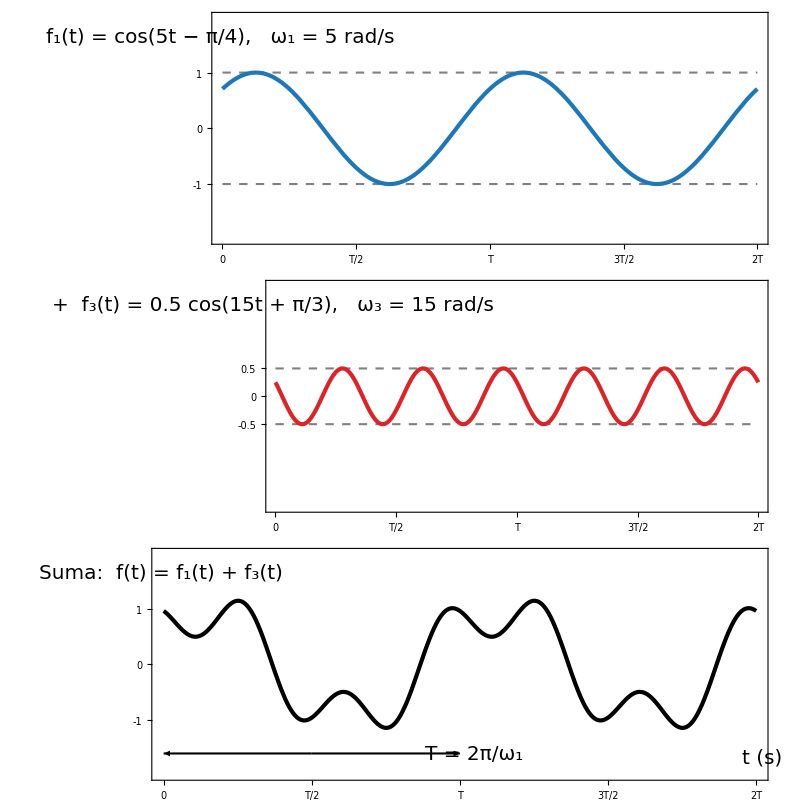

```mathematica
ClearAll[fs,per,f1,f3,f,tLabels,ticksT,ticksY,panel,g1,g3,gS,fig];

fs=20;          (*tamaño de fuente único*)
per=2 Pi/5;     (*período T=2π/ω1*)

f1[t_]:=Cos[5 t-Pi/4];
f3[t_]:=1/2 Cos[15 t+Pi/3];
f[t_]:=f1[t]+f3[t];

tLabels={"0","T/2","T","3T/2","2T"};
ticksT=Table[{(k-1) per/2,Style[tLabels[[k]],fs]},{k,5}];
ticksY[ys_List]:=Table[{y,Style[y,fs]},{y,ys}];

panel[fun_,col_,ys_List,amp_List,label_,extra_List:{}]:=Plot[fun[t],{t,0,2 per},PlotRange->{{0,2 per},{-2,2}},PlotRangePadding->None,PlotStyle->Directive[col,AbsoluteThickness[3]],Background->White,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicks->{{ticksY[ys],None},{ticksT,None}},GridLines->{{per},{0}},GridLinesStyle->Directive[GrayLevel[0.7],AbsoluteThickness[1],Dashing[{0.01,0.01}]],Prolog->{GrayLevel[0.5],AbsoluteThickness[1.5],Dashing[{0.015,0.015}],Table[Line[{{0,s a},{2 per,s a}}],{a,amp},{s,{-1,1}}]},Epilog->{Text[Style[label,fs,Black],Scaled[{0.015,0.9}],{-1,0}],extra},AspectRatio->0.3,ImagePadding->{{75,15},{45,10}}]

(*Primer armónico*)
g1=panel[f1,RGBColor[0.12,0.47,0.71],{-1,0,1},{1},Row[{Subscript["f",1],"(t) = cos(5t − π/4),   ",Subscript["ω",1]," = 5 rad/s"}]];

(*Tercer armónico*)
g3=panel[f3,RGBColor[0.84,0.15,0.16],{-0.5,0,0.5},{0.5},Row[{"+  ",Subscript["f",3],"(t) = 0.5 cos(15t + π/3),   ",Subscript["ω",3]," = 15 rad/s"}]];

(*Suma con indicación del período*)
gS=panel[f,Black,{-1,0,1},{},Row[{"Suma:  f(t) = ",Subscript["f",1],"(t) + ",Subscript["f",3],"(t)"}],{Directive[Black,AbsoluteThickness[1.5]],Arrowheads[0.03],Arrow[{{per/2,-1.6},{0,-1.6}}],Arrow[{{per/2,-1.6},{per,-1.6}}],Text[Style[Row[{"T = 2π/",Subscript["ω",1]}],fs,Black],{per+0.06,-1.6},{-1,0}],Text[Style["t (s)",fs,Black],Scaled[{0.99,0.1}],{1,0}]}];

fig=GraphicsColumn[{g1,g3,gS},Spacings->0,Background->White,ImageSize->800]
```

```mathematica
Export["T2_P1.png",fig,ImageResolution->300]
```

T2_P1.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_P1.png"]]]
```